### Start choosing the example:

```mathematica
t=8;
beta = 0;
A = 0.2;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,1,1},{0,0,0,0},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1},{4,U2}},Switching Costs→{{1,2,4,S1},{1,2,3,S2},{3,2,1,S3},{3,2,4,S4},{4,2,1,S5},{4,2,3,S6}}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->2,U1->5,U2->5, S1->1,S2->2,S3->1,S4->1,S5->2,S6->1}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 0.067048 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.094219,Null}

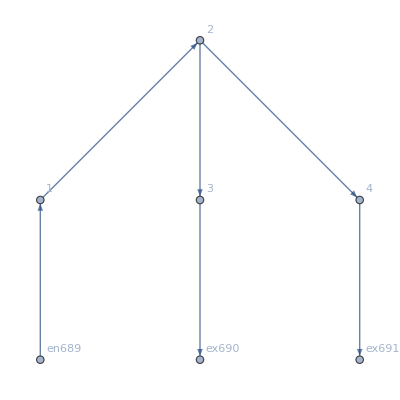

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j692→2.,j693→0.5,j694→1.5,j695→0.5,j696→1.5,j697→2.,j698→0.,j699→0.,j700→0.,j701→0.,j702→0.,j703→0.,jt704→0.,jt705→2.,jt706→0.5,jt707→1.5,jt708→0.,jt709→0.,jt710→0.,jt711→0.,jt712→0.5,jt713→0.,jt714→1.5,jt715→0.,u716→9.5,u717→5.5,u718→6.5,u719→5.,u720→5.,u721→9.5,u722→7.5,u723→5.,u724→5.,u725→5.,u726→5.,u727→9.5|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.151737

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0671729

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0284772

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0119463

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00500928

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00210191

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000882365

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000370491

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000155578

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000653338

<|j692→2.,j693→0.0402416,j694→1.95976,j695→0.0402416,j696→1.95976,j697→2.,j698→0.,j699→0.,j700→0.,j701→0.,j702→0.,j703→0.,jt704→0.,jt705→2.,jt706→0.0402416,jt707→1.95976,jt708→0.,jt709→0.,jt710→0.,jt711→0.,jt712→0.0402416,jt713→0.,jt714→1.95976,jt715→0.,u716→8.083,u717→5.03647,u718→6.03647,u719→5.,u720→5.,u721→8.083,u722→7.03647,u723→5.,u724→5.,u725→5.,u726→5.,u727→8.083|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.144815

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0612099

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0248359

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00996172

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00398705

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0015952

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000638196

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000255323

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000102147

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000408661

<|j692→2.,j693→0.082683,j694→1.91732,j695→0.082683,j696→1.91732,j697→2.,j698→0.,j699→0.,j700→0.,j701→0.,j702→0.,j703→0.,jt704→0.,jt705→2.,jt706→0.082683,jt707→1.91732,jt708→0.,jt709→0.,jt710→0.,jt711→0.,jt712→0.082683,jt713→0.,jt714→1.91732,jt715→0.,u716→8.17459,u717→5.07552,u718→6.07552,u719→5.,u720→5.,u721→8.17459,u722→7.07552,u723→5.,u724→5.,u725→5.,u726→5.,u727→8.17459|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.125314

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.047663

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0171681

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00611646

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00217214

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000770603

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00027329

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000096909

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000343626

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000121843

<|j692→2.,j693→0.171318,j694→1.82868,j695→0.171318,j696→1.82868,j697→2.,j698→0.,j699→0.,j700→0.,j701→0.,j702→0.,j703→0.,jt704→0.,jt705→2.,jt706→0.171318,jt707→1.82868,jt708→0.,jt709→0.,jt710→0.,jt711→0.,jt712→0.171318,jt713→0.,jt714→1.82868,jt715→0.,u716→8.38017,u717→5.15856,u718→6.15856,u719→5.,u720→5.,u721→8.38017,u722→7.15856,u723→5.,u724→5.,u725→5.,u726→5.,u727→8.38017|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00564812

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000467942

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000383919

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.14729×10^-6

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.57992×10^-7

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.11482×10^-8

<|j692→2.,j693→0.453936,j694→1.54606,j695→0.453936,j696→1.54606,j697→2.,j698→0.,j699→0.,j700→0.,j701→0.,j702→0.,j703→0.,jt704→0.,jt705→2.,jt706→0.453936,jt707→1.54606,jt708→0.,jt709→0.,jt710→0.,jt711→0.,jt712→0.453936,jt713→0.,jt714→1.54606,jt715→0.,u716→9.27914,u717→5.44565,u718→6.44565,u719→5.,u720→5.,u721→9.27914,u722→7.44565,u723→5.,u724→5.,u725→5.,u726→5.,u727→9.27914|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[2.89724×10^-15,ComplexInfinity]

<|j692→2.,j693→0.5,j694→1.5,j695→0.5,j696→1.5,j697→2.,j698→0.,j699→0.,j700→0.,j701→0.,j702→0.,j703→0.,jt704→0.,jt705→2.,jt706→0.5,jt707→1.5,jt708→0.,jt709→0.,jt710→0.,jt711→0.,jt712→0.5,jt713→0.,jt714→1.5,jt715→0.,u716→9.5,u717→5.5,u718→6.5,u719→5.,u720→5.,u721→9.5,u722→7.5,u723→5.,u724→5.,u725→5.,u726→5.,u727→9.5|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0374283

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0078923

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00170575

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000366699

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000078923

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000016982

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.65426×10^-6

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.86327×10^-7

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.69203×10^-7

<|j692→2.,j693→0.588118,j694→1.41188,j695→0.588118,j696→1.41188,j697→2.,j698→0.,j699→0.,j700→0.,j701→0.,j702→0.,j703→0.,jt704→0.,jt705→2.,jt706→0.588118,jt707→1.41188,jt708→0.,jt709→0.,jt710→0.,jt711→0.,jt712→0.588118,jt713→0.,jt714→1.41188,jt715→0.,u716→10.0601,u717→5.61741,u718→6.61741,u719→5.,u720→5.,u721→10.0601,u722→7.61741,u723→5.,u724→5.,u725→5.,u726→5.,u727→10.0601|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.231364

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.168221

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.125534

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0909659

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0670511

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0486281

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0356189

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0258629

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0188826

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0137221

<|j692→2.,j693→0.698262,j694→1.30174,j695→0.698262,j696→1.30174,j697→2.,j698→0.,j699→0.,j700→0.,j701→0.,j702→0.,j703→0.,jt704→0.,jt705→2.,jt706→0.698262,jt707→1.30174,jt708→0.,jt709→0.,jt710→0.,jt711→0.,jt712→0.698262,jt713→0.,jt714→1.30174,jt715→0.,u716→11.4665,u717→5.82373,u718→6.82373,u719→5.,u720→5.,u721→11.4665,u722→7.82373,u723→5.,u724→5.,u725→5.,u726→5.,u727→11.4665|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.291563

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.288145

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.285373

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.281854

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.278996

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.275386

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.272449

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.268759

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.265751

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.261992

<|j692→2.,j693→0.527746,j694→1.47225,j695→0.527746,j696→1.47225,j697→2.,j698→0.,j699→0.,j700→0.,j701→0.,j702→0.,j703→0.,jt704→0.,jt705→2.,jt706→0.527746,jt707→1.47225,jt708→0.,jt709→0.,jt710→0.,jt711→0.,jt712→0.527746,jt713→0.,jt714→1.47225,jt715→0.,u716→12.2039,u717→5.85812,u718→6.85812,u719→5.,u720→5.,u721→12.2039,u722→7.85812,u723→5.,u724→5.,u725→5.,u726→5.,u727→12.2039|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.419684

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.718511

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«5 more identical outputs»

<|j692→2.,j693→0,j694→2.,j695→0.,j696→2.,j697→2.,j698→0.,j699→0.,j700→0.,j701→0.,j702→0.,j703→0.,jt704→0.,jt705→2.,jt706→0,jt707→2.,jt708→0.,jt709→0.,jt710→0.,jt711→0.,jt712→0.,jt713→0.,jt714→2.,jt715→0.,u716→14.9909,u718→7.,u719→5.,u720→5.,u721→14.9909,u722→8.,u723→-4.99091+1. u717,u724→5.,u725→5.,u726→5.,u727→14.9909|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.549253

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.805485

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«5 more identical outputs»

<|j692→2.,j693→0,j694→2.,j695→0.,j696→2.,j697→2.,j698→0.,j699→0.,j700→0.,j701→0.,j702→0.,j703→0.,jt704→0.,jt705→2.,jt706→0,jt707→2.,jt708→0.,jt709→0.,jt710→0.,jt711→0.,jt712→0.,jt713→0.,jt714→2.,jt715→0.,u716→17.8941,u718→7.,u719→5.,u720→5.,u721→17.8941,u722→8.,u723→-7.89413+1. u717,u724→5.,u725→5.,u726→5.,u727→17.8941|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.723085

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«16 more identical outputs»

<|j653→2.,j654→2.,j655→0.,j656→2.,j657→0.,j658→2.,j659→0.,j660→0.,j661→0.,j662→0.,j663→0.,j664→0.,jt665→0.,jt666→2.,jt667→2.,jt668→0.,jt669→0.,jt670→0.,jt671→0.,jt672→0.,jt673→2.,jt674→0.,jt675→0.,jt676→0.,u677→23.3732,u678→7.,u679→7.,u680→5.,u681→6.,u682→23.3732,u683→7.,u684→5.,u685→-7.3732,u686→5.,u687→6.,u688→23.3732|>